# Tao Whitepaper : A project research page

A selection of ideas to explore . . .

# Barry White: Tree Calculus

## Introduction

Programs in the tree calculus are represented as binary trees.

My aim is to by the end of the paper decide on whether or not to engage in a full implementation of a programming language based on the mathematics introduced so far in his paper.

Fundamentals: How does the calculus work? How do we know it is Turing Complete?

Problems Solved: What does tree calculus provide us with that we didn’t already have?

## Fundamentals

## Trees

Tree Calculus is more accurately called binary-tree calculus.

In tree calculus computations are unlabelled, finitely branching trees. The nodes of the tree are instances of the ‘node’ operator, Δ. The edges are left associative applications.

### Node Operator: Ternary operations

```mathematica
ΔΔyz := y
```

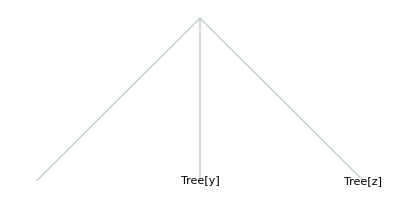
-Graphics-→Tree[z]

```mathematica
Tree[{Tree[{}], Tree[y], Tree[z]}]  -> Tree[z]
```

```mathematica
Δ(Δx)yz := (yz)(xz)
```

$Failed

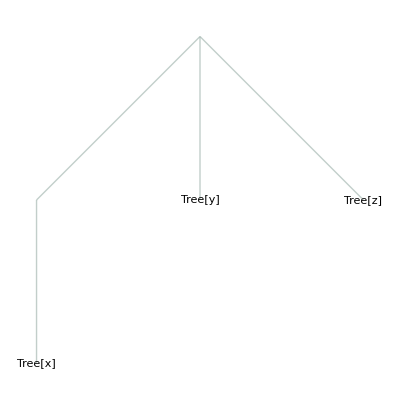
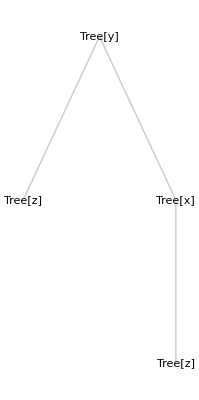
-Graphics-→-Graphics-

```mathematica
Tree[{Tree[{Tree[x]}], Tree[y],Tree[z]}] ->Tree[Tree[y],{Tree[z], Tree[Tree[x],{Tree[z]}]}]
```

```mathematica
Δ(Δwx)yz:=zwx
```

$Failed

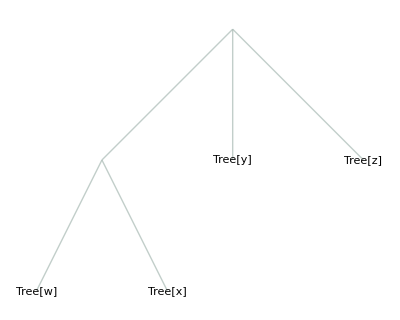
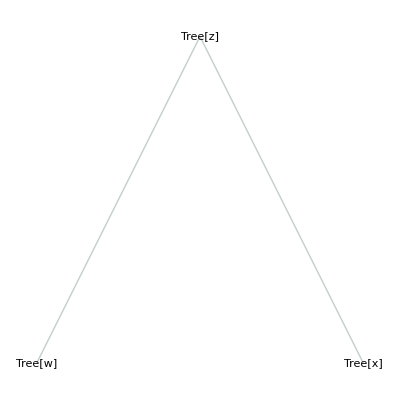
-Graphics-→-Graphics-

```mathematica
Tree[{Tree[{Tree[w],Tree[x]}], Tree[y], Tree[z]}] -> Tree[Tree[z], {Tree[w], Tree[x]}]
```

## More Programs

```mathematica
Hyperlink["https://community.wolfram.com/groups/-/m/t/2316020"]
```

https://community.wolfram.com/groups/-/m/t/2316020

## Problems Solved

I have high hopes for this projects future, it boasts the potential to create some fascinating “self-understanding” code.

# Grothendieck: Colossus of Ideas

## Fundamental ideas

The father of modern algebraic geometry, also with contributions to commutative algebra, homological algebra, sheaf theory and category theory .

Let’s approach these topics with constructivist intent!

## Algebraic geometry

```mathematica
Hyperlink["https://www.maths.ox.ac.uk/about-us/departmental-art/theory/algebraic-geometry#:~:text=%20Algebraic%20Geometry%20%201%20Introduction.%20As%20its,are%20a%20very%20powerful%20and%20useful...%20More%20"]
```

https://www.maths.ox.ac.uk/about-us/departmental-art/theory/algebraic-geometry#:~:text=%20Algebraic%20Geometry%20%201%20Introduction.%20As%20its,are%20a%20very%20powerful%20and%20useful...%20More%20

Concerns curves or surfaces which can be viewed as both geometric objects, and as solutions to algebraic equations.

For example,

```mathematica
poly0[x_,y_]:= x^2 - x^2*y^2 + y^3 +x*y -1;
```

```mathematica
poly0[1,4]
```

52

```mathematica
Plot3D[poly0[x,y],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
solutions0 = Solve[poly0[x,y]==0, {x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→(y-√(4-3 y^2-4 y^3+4 y^5))/(2 (-1+y^2))},{x→(y+√(4-3 y^2-4 y^3+4 y^5))/(2 (-1+y^2))},{x→-2,y→-1},{x→0,y→1}}

```mathematica
inflections0 = ResourceFunction["StationaryPoints"][poly0[x,y],{x,y}]
```

<|Minima→{{Root-1.00Root[-166319-371124 #1-180576 #1^2+100224 #1^3+103680 #1^4+27648 #1^5&,1]-1.002540447726378,{x→AlgebraicNumber-0.0918AlgebraicNumber[Root[-6-36 #1-18 #1^2+#1^5&,2],{0,1/2,0,0,0}]-0.0917552496693197,y→AlgebraicNumber0.178AlgebraicNumber[Root[-6-36 #1-18 #1^2+#1^5&,2],{6/37,-2/37,6/37,-1/37,1/222}]0.17771477164189556}}},Saddle→{{-1,{x→0,y→0}},{Root-0.896Root[-166319-371124 #1-180576 #1^2+100224 #1^3+103680 #1^4+27648 #1^5&,2]-0.8958543317225551,{x→AlgebraicNumber-0.749AlgebraicNumber[Root[-6-36 #1-18 #1^2+#1^5&,1],{0,1/2,0,0,0}]-0.7489149381405209,y→AlgebraicNumber0.720AlgebraicNumber[Root[-6-36 #1-18 #1^2+#1^5&,1],{6/37,-2/37,6/37,-1/37,1/222}]0.7204290928928371}},{Root1.53Root[-166319-371124 #1-180576 #1^2+100224 #1^3+103680 #1^4+27648 #1^5&,3]1.5289794071085232,{x→AlgebraicNumber1.56AlgebraicNumber[Root[-6-36 #1-18 #1^2+#1^5&,3],{0,1/2,0,0,0}]1.5567438972903649,y→AlgebraicNumber1.17AlgebraicNumber[Root[-6-36 #1-18 #1^2+#1^5&,3],{6/37,-2/37,6/37,-1/37,1/222}]1.173404352761867}}}|>

Specifically, we are interested in the points such as singularities, inflections and infinities ...

Let’s consider a different, slightly more interesting function and do some analytics:

```mathematica
poly1[x_,y_]:= (x/y^2)+y^7/x - y*x;
```

```mathematica
Plot3D[poly1[x,y], {x, -40,40},{y,-40,40}]
```

-Graphics3D-

```mathematica
singularities1 = FunctionSingularities[poly1[x,y],{x,y}]
```

x==0||y==0

```mathematica
inflections1 = ResourceFunction["StationaryPoints"][poly1[x,y],{x,y}]
```

<|Saddle→{{-1/8 √3 5^(5/6),{x→-(5 √(5/3))/8,y→5^(1/3)/2}},{1/8 √3 5^(5/6),{x→(5 √(5/3))/8,y→5^(1/3)/2}}}|>

## Commutative Algebra

## Homological Algebra

## Sheaf Theory

## Category Theory

# The Ancient History

```mathematica
Hyperlink["https://en.wikipedia.org/wiki/Plimpton_322"]
```

https://en.wikipedia.org/wiki/Plimpton_322